```mathematica
Needs["ErrorBarPlots`"]
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Rasterize[Show[g,PlotRangePadding->0,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res]/.Raster[data_,rect_,rest__]:>Raster[data,Transpose@OptionValue[AbsoluteOptions[g,PlotRange],PlotRange],rest],Sequence@@Options[g],Sequence@@Options[g,PlotRange]]
file=OpenRead["../gri30.cti"];
test=ReadList[file,"String"];
Close[file];
slst=StringSplit[Extract[test,Position[test,u_/;StringQ[u]&&First[StringSplit[u,"("]]=="species"]],"\""][[All,2]];
alst=Partition[#,2]&/@StringSplit[StringTrim[StringSplit[Extract[test,Position[test,u_/;StringQ[u]&&First[StringSplit[u,"("]]=="species"]+1],"\""][[All,2]]],{"  ",":"}];
sensitivities=Flatten[Import["dilute0/dilute0ms.dat"]];
```

/Users/zack/Documents/ignition/cantera/dilute

### Full model ignition peaks

```mathematica
Length[concentrations]
Length[concentrations[[Oind]]]
```

53

5000

dilute0/dilute0

{0.094924,0.126776,0.179856,0.0167348,0.0234416,0.0334884,0.0042168,0.00577216,0.00819672,0.0141568,0.01524,0.018072,0.00190076,0.00233956,0.0030938,0.000519792,0.000662376,0.00089604,0.004008,0.00371332,0.0037924,0.000428796,0.000436304,0.000494508,0.00010412,0.000114356,0.000138432}

{0.0184213,0.0154867,0.000274635,0.0132104,0.0130542,0.000194134,0.00698259,0.0091857,0.0000970267,0.020088,0.0167101,0.000423005,0.0158591,0.0147941,0.000324329,0.00977441,0.0114635,0.000198369,0.0215815,0.0179512,0.000592459,0.0182236,0.0163849,0.000497371,0.0126188,0.0134242,0.000345257}

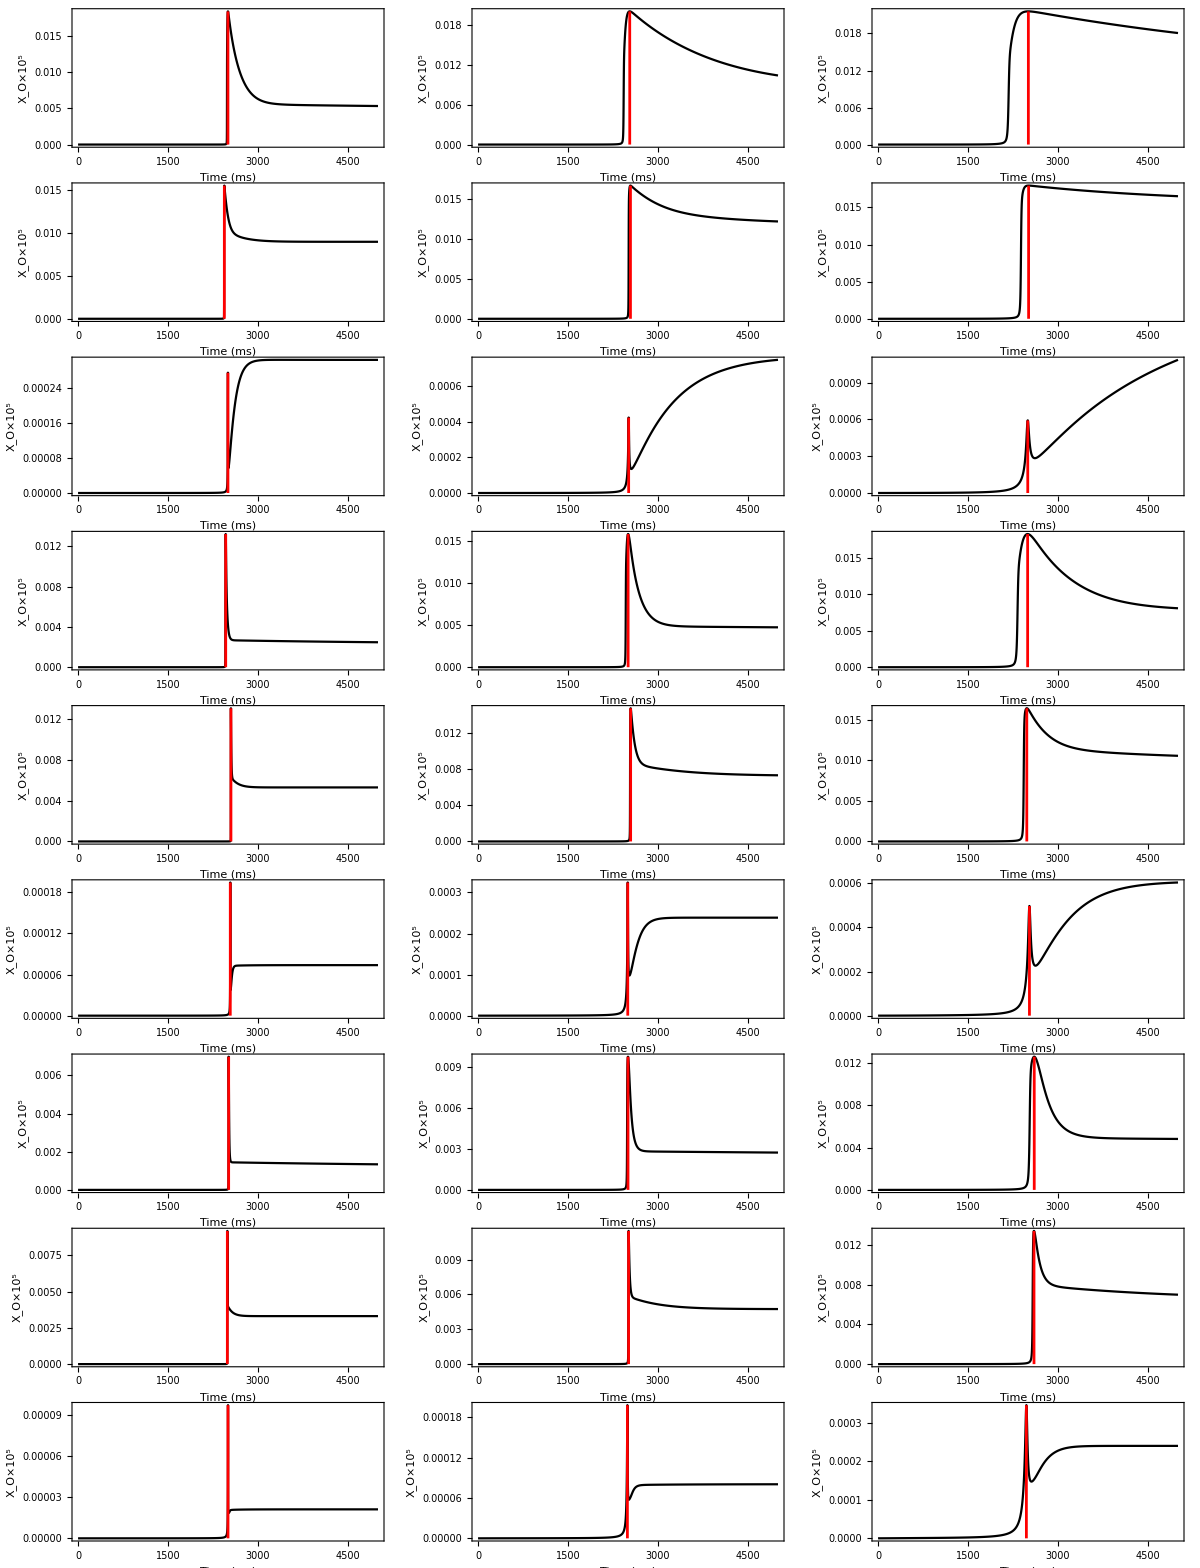

```mathematica
itimes={};
imaxes={};
plots={};
ns=53;
filebase="dilute0/dilute0"
species=Import[filebase<>"_species.dat"][[1]];
Monitor[Do[
times=BinaryReadList[filebase<>"_times_"<>ToString[n]<>".npy","Real64"][[17;;-1]];
Oind=First@FirstPosition[species,"O"];
concentrations=Transpose[Partition[BinaryReadList[filebase<>"_moles_"<>ToString[n]<>".npy","Real64"][[17;;-1]],ns]];
ind=First@FirstPosition[Sign[Differences[concentrations[[Oind]]]],-1];
AppendTo[itimes,times[[ind]]];
AppendTo[imaxes,concentrations[[Oind,ind]]];
AppendTo[plots,
ListPlot[concentrations[[Oind]],PlotStyle->Directive[Black],PlotRange->All,Joined->True,LabelStyle->Directive[16],Axes->False,Frame->True,FrameLabel->{"Time (ms)",DisplayForm[RowBox[{Subscript[X,O],"×",10^HoldForm[5]}]]},ImagePadding->{{75,5},{75,5}},ImageSize->250,AspectRatio->1,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],Epilog->{Red,AbsoluteThickness[2],Line[{{ind,0},{ind,concentrations[[Oind,ind]]}}]}]];,{n,0,26}],n]
2*itimes
imaxes
Multicolumn[plots,3]
```

```mathematica
ScientificForm[itimes/10^-3,2]
ScientificForm[imaxes,2]
```

{4.7×10^1,6.3×10^1,9.×10^1,8.4,1.2×10^1,1.7×10^1,2.1,2.9,4.1,7.1,7.6,9.,9.5×10^-1,1.2,1.5,2.6×10^-1,3.3×10^-1,4.5×10^-1,2.,1.9,1.9,2.1×10^-1,2.2×10^-1,2.5×10^-1,5.2×10^-2,5.7×10^-2,6.9×10^-2}

{1.8×10^-2,1.5×10^-2,2.2×10^-4,1.3×10^-2,1.3×10^-2,1.6×10^-4,5.3×10^-3,9.3×10^-3,8.8×10^-5,2.×10^-2,1.7×10^-2,4.2×10^-4,1.6×10^-2,1.5×10^-2,3.1×10^-4,9.8×10^-3,1.1×10^-2,2.×10^-4,2.2×10^-2,1.8×10^-2,5.9×10^-4,1.8×10^-2,1.6×10^-2,5.×10^-4,1.3×10^-2,1.3×10^-2,3.5×10^-4}

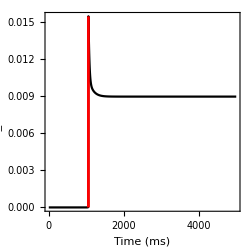

```mathematica
plots[[2]]
```

### Graph plots

3419

{RGBColor[Rational[1, 3], Rational[1, 3], 1],RGBColor[1, Rational[1, 3], Rational[1, 3]]}

{RGBColor[0.165698, 0.282261, 0.936187],RGBColor[0.845274, 0.369528, 0.19115]}

{RGBColor[0.431296, 0.709773, 0.927077],RGBColor[0.898695, 0.686452, 0.6785475]}

{RGBColor[Rational[1, 3], Rational[1, 3], 1],RGBColor[1, Rational[1, 3], Rational[1, 3]]}

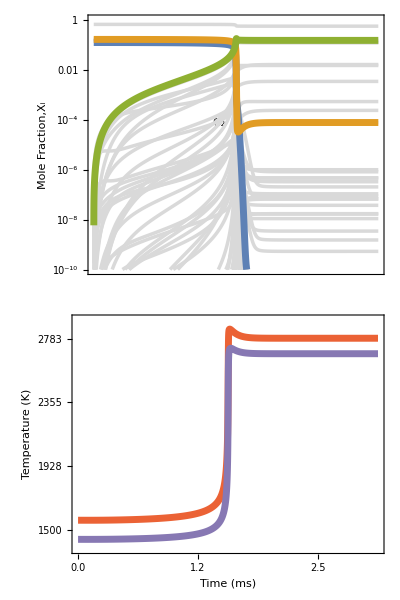

```mathematica
filebase="dilute0/dilute0";
Nt=5000.;
file=OpenRead[filebase<>"obs_"<>ToString[13]<>".dat"];
strings=StringSplit[#," "]&/@ReadList[file,String];
Close[file];
lst=Join[{strings[[1]]},Transpose[{(StringSplit[#,":"]&/@#&/@(StringSplit[#,","]&/@(StringTrim[#,"}"]&/@(StringTrim[#,"{"]&/@Flatten/@(StringSplit[#,"->"]&/@strings[[2;;Length[strings],1]]))))),Internal`StringToDouble/@#&/@(strings[[2;;Length[strings],2;;Length[strings[[2]]]]])}]];

imagePadding2={{75,75},{1,1}};
imgSize2={500,250};
imagePadding1={{75,75},{50,1}};
imgSize1={500,290};
imgSize3={440*(2.2)/(1.3),440};

sptime[text_]:=First@FirstPosition[Accumulate[10^-12+Cases[lst[[1;;-1]],u_/;u[[1]]=={{{"["<>text<>"]"}}}][[1,2]]]/Total[10^-12+Cases[lst[[1;;-1]],u_/;u[[1]]=={{{"["<>text<>"]"}}}][[1,2]]],u_/;u>0.5]/Nt;
sptimemin=Min[sptime/@lst[[1,2;;-1]]];
sptimemax=Max[sptime/@lst[[1,2;;-1]]];
spcol[text_]:=Blend[{Cyan,Orange},(sptime[text]-sptimemin)/(sptimemax-sptimemin)];
vsize[text_]:=0.005+0.08*(Log[Max[Mean[Cases[lst[[1;;Length[lst]]],u_/;u[[1]]=={{{"["<>text<>"]"}}}][[1,2]]],10^-8]]/Log[10]+8)/8;

Oind=First@FirstPosition[lst[[All,1]],"[O]"];
nmax=Length[lst[[2,2]]];
nspecies=Length[lst[[1]]]-1;
nreactions=Length[lst]-nspecies-4;
tmax=Max[lst[[2,2]]]/10^-3;
Tmax=Max[lst[[3,2]]];
Tmin=Min[lst[[3,2]]];
Pmax=Max[lst[[4,2]]];
Pmin=Min[lst[[4,2]]];
tmax=Max[lst[[2,2]]]/10^-3;
timin=Max[Last@FirstPosition[lst[[5;;4+nreactions,2]],Max[lst[[5;;4+nreactions,2]]]]-150,5];
timax=Min[Last@FirstPosition[lst[[5;;4+nreactions,2]],Max[lst[[5;;4+nreactions,2]]]]+150,nmax];
reactantnames={"CH4","O2","N2"};
productnames={"CO2","H2O","CO"};
ohintermediates={"H2","H","O","OH"};
cmax=1.1*Max[{lst[[First@FirstPosition[lst[[1;;Length[lst],1]],"[H2O]"]]][[2]],lst[[First@FirstPosition[lst[[1;;Length[lst],1]],"[CH4]"]]][[2]],lst[[First@FirstPosition[lst[[1;;Length[lst],1]],"[O2]"]]][[2]]}];
cplots={"CH4","O2","H2O"};
ccplots=ColorData[97,"ColorList"][[1;;3]];
p1=ListLogPlot[Join[lst[[-nspecies;;-1,2]],(lst[[First@FirstPosition[lst[[1;;Length[lst],1]],"["<>#<>"]"],2]]*(0.75+0.5*(First@FirstPosition[cplots,#]-1)/(Length[cplots]-1)))&/@cplots],Joined->True,PlotRange->{10^-10,1},LabelStyle->Directive[16,Black],Axes->False,Frame->True,FrameLabel->{None,DisplayForm[RowBox[{"Mole Fraction,",Subscript[ X,i]}]]},FrameTicks->{{Automatic,{}},Table[{i,""},{i,0,(nmax-1),(nmax-1)/5}]},PlotStyle->Join[ConstantArray[Directive[Thickness[0.005],LightGray],nspecies],Directive[Thickness[0.01],#]&/@ccplots],Prolog->Join[Inset[Framed[Style[DisplayForm[ToBoxes@Row[Subscript[#[[1]],#[[2]]/."1"->""]&/@SortBy[Extract[alst,FirstPosition[slst,#[[1]]]],First]]],16,#[[2]]],Background->None,FrameStyle->None],{2200,Log[lst[[First@FirstPosition[lst[[1;;Length[lst],1]],"["<>#[[1]]<>"]"],2,-1]]]}]&/@Transpose[{cplots,ccplots}]],ImagePadding->imagePadding2,ImageSize->imgSize2,AspectRatio->Last[imgSize1]/First[imgSize1],FrameStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRangeClipping->False];
p2=ListPlot[{(lst[[3,2]]-Tmin)/(Tmax-Tmin)+0.05,(lst[[4,2]]-Pmin)/(Pmax-Pmin)-0.05},Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[4]],Thickness[0.01]],Directive[ColorData[97,"ColorList"][[5]],Thickness[0.01]]},PlotRange->{-0.1,1.1},LabelStyle->Directive[16,Black],Axes->False,Frame->True,FrameLabel->{{Style["Temperature (K)",ColorData[97,"ColorList"][[4]]],Style["Pressure (atm)",ColorData[97,"ColorList"][[5]]]},{"Time (ms)",None}},FrameTicks->{{Table[{(T-Tmin)/(Tmax-Tmin),Style[Round[T],ColorData[97,"ColorList"][[4]]]},{T,Tmin,Tmax,(Tmax-Tmin)/3}],Table[{(P-Pmin)/(Pmax-Pmin),Style[PaddedForm[P/101325.,{3,2}],ColorData[97,"ColorList"][[5]]]},{P,Pmin,Pmax,(Pmax-Pmin)/3}]},{Table[{i,PaddedForm[tmax*i/(nmax-1),{4,1}]},{i,0,(nmax-1),(nmax-1)/5}],{}}},ImagePadding->imagePadding1,ImageSize->imgSize1,AspectRatio->Last[imgSize1]/First[imgSize1],FrameStyle->Directive[Black,AbsoluteThickness[1.5]]];
(* Possible bimolecular interactions *)
reacs=Flatten[Table[{i,j},{i,1,Length[alst]},{j,i,Length[alst]}],1];
atoms=DeleteDuplicates[Flatten[alst[[All,All,1]]]];
acount[r_]:=(Total[ToExpression/@Cases[Flatten[alst[[r[[{1,2}]]]],1],u_/;u[[1]]==#][[All,2]]]&/@atoms);
test=acount/@reacs;
test2=Cases[Position[test,#]&/@DeleteDuplicates[test],u_/;Length[u]>1];
stoipairs=slst[[#]]&/@#&/@(Extract[reacs,#]&/@test2);
stoipairs2=Flatten[Subsets[#,{2,2}]&/@stoipairs,1];
Total[Binomial[#,2]&/@(Length/@stoipairs)]
colors={Lighter[Blue],Lighter[Red]}
colors={ColorData["LightTemperatureMap"][0],ColorData["LightTemperatureMap"][1]}
colors={ColorData["Pastel"][1],ColorData["Pastel"][1/4]}
colors={Lighter[Blue],Lighter[Red]}
rlst=Import[filebase<>"norms.dat"];
sensitivities=Flatten[Import[filebase<>"ms.dat"]];
isensitivities=Flatten[Import[filebase<>"mi.dat"]];
Grid[{{p1},{p2}}]
```

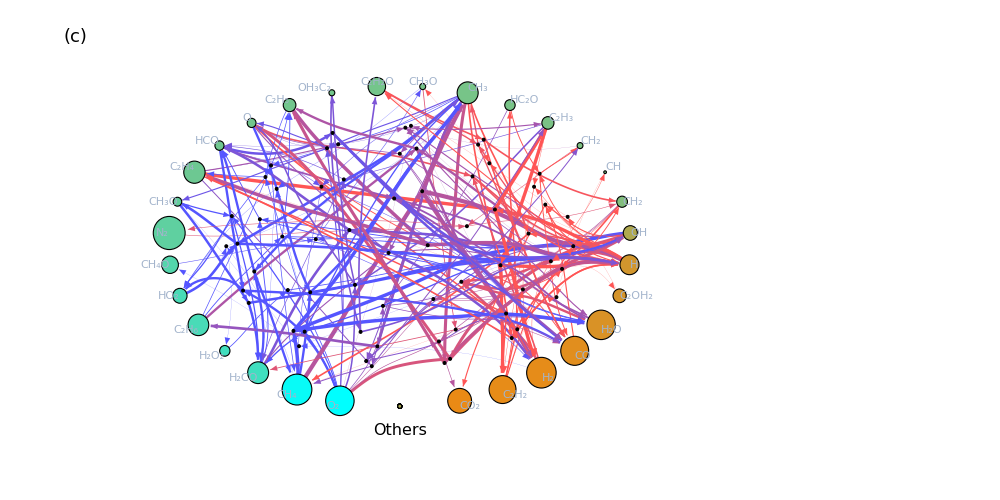
-Graphics- | -Graphics-

```mathematica
r1=1.5;
r2=1;
weights=Mean/@lst[[5;;4+nreactions,2,All]];
weights2=First@FirstPosition[Abs[#],Max[Abs[#]]]&/@lst[[5;;4+nreactions,2,All]]/Nt;
reactants=Flatten/@lst[[5;;4+nreactions,1,1,All,1]];
products=Flatten/@lst[[5;;4+nreactions,1,2,All,1]];
wscale=Max[Abs[weights]];
ethrs=Mean[Abs[weights]]/2;
ethick=0.003;
shown=Flatten[Position[weights,u_/;Abs[u]>ethrs]];
edges=Table[If[weights[[i]]>0,Join[Table[reactants[[i,j]]->i,{j,1,Length[reactants[[i]]]}],Table[i->products[[i,j]],{j,1,Length[products[[i]]]}]],Join[Table[i->reactants[[i,j]],{j,1,Length[reactants[[i]]]}],Table[products[[i,j]]->i,{j,1,Length[products[[i]]]}]]],{i,1,nreactions}];
species=SortBy[DeleteDuplicates[Join[Flatten[products],Flatten[reactants]]],spcol[#]&];
center=DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]];
centerspecies=SortBy[Complement[DeleteDuplicates[DeleteDuplicates[Join[Flatten[edges[[shown,All,1]]],Flatten[edges[[shown,All,2]]]]]],Range[nreactions]],spcol[#]&];
centerreactions=Complement[center,centerspecies];
bottomspecies=SortBy[Complement[species,centerspecies],spcol[#]&];
bottomreactions=Complement[Range[nreactions],centerreactions];
rvcs=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]>ethrs]],GraphLayout->"SpiralEmbedding"]];
rvcs2=GraphEmbedding[PathGraph[Flatten[Position[weights,u_/;Abs[u]<=ethrs]],GraphLayout->"SpiralEmbedding"]];
{xmax,xmin,ymax,ymin}={Max[rvcs[[All,1]]],Min[rvcs[[All,1]]],Max[rvcs[[All,2]]],Min[rvcs[[All,2]]]};
{xmax2,xmin2,ymax2,ymin2}={Max[rvcs2[[All,1]]],Min[rvcs2[[All,1]]],Max[rvcs2[[All,2]]],Min[rvcs2[[All,2]]]};
transform[p_]:=1.5*{r1,r2}*{(p[[2]]-ymin)/(ymax-ymin)-1/2,(p[[1]]-xmin)/(xmax-xmin)-1/2};
transform2[p_]:=1.5*{r1,r2}*{(p[[2]]-ymin2)/(ymax2-ymin2)-1/2,(p[[1]]-xmin2)/(xmax2-xmin2)-1/2};
trange=Quantile[Extract[weights2,Position[weights,u_/;Abs[u]>ethrs]],{0.25,0.75}];
eweight[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights[[edge[[1]]]],weights[[edge[[2]]]]];
ecolor[edge_]:=If[MemberQ[Range[nreactions],edge[[1]]],weights2[[edge[[1]]]],weights2[[edge[[2]]]]];
vsize[text_]:=0.005+0.08*(Log[Max[Mean[Cases[lst[[1;;Length[lst]]],u_/;u[[1]]=={{{"["<>text<>"]"}}}][[1,2]]],10^-8]]/Log[10]+8)/8;
sizes={1.0,0.1,0.01,0.001,0.0001};
wsizes=Table[z/.First@Solve[(Log[Abs[z/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])==i*1.0/5,z],{i,5,1,-1}];
vcs=Join[Table[centerspecies[[i]]->{r1*Cos[3*Pi/2-Pi/12-(2*Pi-2*Pi/12)*(i-1)/(Length[centerspecies]-1)],r2*Sin[3*Pi/2-Pi/12-(2*Pi-2*Pi/12)*(i-1)/(Length[centerspecies]-1)]},{i,1,Length[centerspecies]}],
Table[bottomspecies[[i]]->{0,-r2},{i,1,Length[bottomspecies]}],Table[i->If[MemberQ[centerreactions,i],transform[rvcs[[First@FirstPosition[SortBy[Flatten[Position[weights,u_/;Abs[u]>ethrs]],weights2[[#]]&],i]]]],transform2[rvcs2[[First@FirstPosition[SortBy[Flatten[Position[weights,u_/;Abs[u]<=ethrs]],weights2[[#]]&],i]]]]],{i,nreactions}]];
p0=Graph[Join[species,shown],Flatten[edges],GraphLayout->{"EdgeLayout"->"DividedEdgeBundling"},VertexCoordinates->vcs,VertexLabels->(#->If[ValueQ[Element[#,Integers]],None,If[MemberQ[centerspecies,#],If[0.0015*ImageDimensions[Rasterize[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Sort[Extract[alst,FirstPosition[slst,#]]]]],16,Black],Background->LightGray,FrameStyle->None,RoundingRadius->5,ContentPadding->False]]][[1]]<vsize[#]&&False,Placed[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Extract[alst,FirstPosition[slst,#]]]],16,Black],Background->None,FrameStyle->None,RoundingRadius->5,Alignment->Center],Center],Placed[Framed[Style[DisplayForm[ToBoxes@Row[If[#[[2]]≠"1",Subscript[#[[1]],#[[2]]],#[[1]]]&/@Extract[alst,FirstPosition[slst,#]]]],16,Black],Background->None,FrameStyle->None,RoundingRadius->5,Alignment->Center,ContentPadding->False],{{1/2,1/2},{1/2,1/2}-(#/Norm[#]/.vcs)}]],None]]&/@Join[species,Range[nreactions]]),VertexStyle->(#->If[ValueQ[Element[#,Integers]],{If[MemberQ[bottomreactions,#],{Opacity[0],EdgeForm[None]},{Opacity[1],EdgeForm[Black]}],Black},If[MemberQ[centerspecies,#],{spcol[#],EdgeForm[Black]},{Opacity[1.0],Blend[spcol/@bottomspecies],EdgeForm[Black]}]]&/@Join[species,Range[nreactions]]),
VertexSize->(#->If[ValueQ[Element[#,Integers]],{"Scaled",0.005},If[MemberQ[centerspecies,#],{"Scaled",0.7*vsize[#]},{"Scaled",0.7*Mean[vsize/@bottomspecies]}]]&/@Join[species,Range[nreactions]]),EdgeStyle->(#-> If[Abs[eweight[#]]<=ethrs,{Directive[Opacity[0]]},{Directive[Opacity[1.0]],Directive[Blend[colors,(ecolor[#]-trange[[1]])/(trange[[2]]-trange[[1]])]],Thickness[Abs[ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Arrowheads[{{Abs[10*ethick*(Log[Abs[eweight[#]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])],1.0}}]}]&/@Flatten[edges]),EdgeShapeFunction->(If[Position[vcs,First[#]]≠{},{Arrow[#,{0.0,1.5*vsize[vcs[[FirstPosition[N[vcs],Last[#]][[1]],1]]]}]},{Arrow[#,{0.0,0.01}]}]&),ImageSize->{1000,500}];
p=Show[p0,Prolog->{Inset[Grid[{{Graphics[Text[Style["Nodes",16],{0,0}],ImageSize->{125,50}],Graphics[Text[Style["Links",16],{0,0}],ImageSize->{125,50}]},{MatrixPlot[Table[Blend[{Cyan,Orange},(y-sptimemin)/(sptimemax-sptimemin)],{y,sptimemin,sptimemax,(sptimemax-sptimemin)/100},{x,1,100}],AspectRatio->10,ImageSize->{125,175},ImagePadding->{{90,15},{10,5}},FrameTicks->{{Table[{i,PaddedForm[(sptimemin+(i-1)*(sptimemax-sptimemin)/100)*lst[[2,2,-1]]/10^-3,{3,3}]},{i,1,101,20}],None},{None,None}},PlotRangePadding->None,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{"Species Time (ms)",None}},RotateLabel->True,DataReversed->{True,True}],MatrixPlot[Table[Directive[Opacity[1.0],Blend[colors,(y-trange[[1]])/(trange[[2]]-trange[[1]])]],{y,trange[[1]],trange[[2]],(trange[[2]]-trange[[1]])/100},{x,1,100}],AspectRatio->10,ImageSize->{125,175},ImagePadding->{{5,90},{10,5}},FrameTicks->{{None,Table[{i,PaddedForm[(trange[[1]]+(i-1)*(trange[[2]]-trange[[1]])/100)*lst[[2,2,-1]]/10^-3,{4,4}]},{i,1,101,20}]},{None,None}},PlotRangePadding->None,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,"Reaction Time (ms)"}},RotateLabel->True,DataReversed->{True,True}]},{Graphics[{{Table[{EdgeForm[Black],White,Disk[{-1.0,-1.25*i},12*(0.005+0.08*(Log[sizes[[i]]]/Log[10]+8)/8)],Black,Text[Style[With[{n=i},HoldForm[10^(-n)]],16],{-2.8,-1.25*i}]},{i,1,Length[sizes]}]},Rotate[Text[Style["Mole Fraction",16],{-4.0,-4}],Pi/2]},PlotRange->{{-5,0.1},{-8,0}},ImageSize->{125,175}],Graphics[{{Table[{Thickness[10*Abs[ethick*(Log[Abs[wsizes[[i]]/wscale]]-Log[Abs[ethrs/wscale]])/(0-Log[Abs[ethrs/wscale]])]],Line[{{1,-1.25*i},{2,-1.25*i}}],Text[Style[PaddedForm[wsizes[[i]],{2,2}],16],{3,-1.25*i}]},{i,1,Length[sizes]}]},Rotate[Text[Style[DisplayForm[RowBox[{"Rate ","(","mol ",Superscript["m",-3],Superscript["ms",-1],")"}]],16],{4.9,-4}],Pi/2]},PlotRange->{{0.5,6},{-8,0}},ImageSize->{125,175}]}}],{2.6,0.0}],Text[Style["Others",16],{0,-r2-0.15}]},ImageSize->{1000,500},PlotRange->{{-2,3.3},{-1.3,1.25}},PlotRangePadding->None];
p3=Grid[{{Grid[{{Show[p1,Epilog->{Inset[Style["(a)",18],ImageScaled[{0,1}],Scaled[{0,1}]]},PlotRangeClipping->False]},{Show[p2,Epilog->{Inset[Style["(b)",18],ImageScaled[{0,1}],Scaled[{0,1}]]},PlotRangeClipping->False]}},Alignment->Left,Spacings->0],Show[p,Epilog->{Inset[Style["(c)",18],Scaled[{0,1}],Scaled[{0,1}]]}]}},Spacings->0]
Export["fig1.pdf",p3,LineBreakWithin->False];
```

### Correlations, density plots, and histograms

```mathematica
rlst1=Import["dilute0/norms.dat"];
rlst2=Import["dilute2/norms.dat"];
Table[Count[rlst1,u_/;u[[3]]==remove&&u[[4]]==keep&&(u[[6]]=="failed"||Abs[Log[u[[6]]]/Log[10]]>1)],{keep,10,160,30},{remove,10,160,30}]
Table[Count[rlst2,u_/;u[[3]]==remove&&u[[4]]==keep&&(u[[6]]=="failed"||Abs[Log[u[[6]]]/Log[10]]>1)],{keep,10,160,30},{remove,10,160,30}]
diff=DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1,{rlst1[[i,1]],rlst1[[i,2]],rlst1[[i,3]],rlst1[[i,4]],rlst1[[i,5]],Log[rlst1[[i,6]]/rlst2[[i,6]]]/Log[10], Log[(rlst1[[i,6]]+rlst2[[i,6]])/2]/Log[10],rlst1[[i,7]]-rlst2[[i,7]]}],{i,1,Length[rlst1]}],Null];
Table[Count[diff,u_/;u[[3]]==remove&&u[[4]]==keep],{keep,10,160,30},{remove,10,160,30}]
```

{{40,117,186,244,399,560},{1,12,22,40,74,79},{0,0,0,0,1,2},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

{{25,71,147,296,488,733},{1,16,32,46,64,91},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

{{1957,1852,1733,1545,1299,1025},{1999,1979,1957,1929,1883,1841},{2000,2000,2000,2000,1999,1998},{2000,2000,2000,2000,2000,2000},{2000,2000,2000,2000,2000,2000},{2000,2000,2000,2000,2000,2000}}

```mathematica
Correlation[DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1,rlst1[[i,6]]],{i,1,Length[rlst1]}],Null],DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1,rlst2[[i,6]]],{i,1,Length[rlst1]}],Null]]
```

0.612532

```mathematica
Monitor[Table[Correlation[Cases[DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1,rlst1[[i]]],{i,1,Length[rlst1]}],Null],u_/;u[[3]]==remove&&u[[4]]==keep][[All,6]],Cases[DeleteCases[Table[If[rlst1[[i,6]]≠"failed"&&rlst2[[i,6]]≠"failed"&&Abs[Log[rlst1[[i,6]]]/Log[10]]<1&&Abs[Log[rlst2[[i,6]]]/Log[10]]<1,rlst2[[i]]],{i,1,Length[rlst2]}],Null],u_/;u[[3]]==remove&&u[[4]]==keep][[All,6]]],{keep,10,160,30},{remove,10,160,30}],{keep,remove}]
```

{{0.468416,0.526393,0.476045,0.412277,0.206064,0.26268},{0.0494812,0.122914,0.124297,0.127399,0.163684,0.183623},{0.105296,0.102823,0.12037,0.223921,0.331251,0.471247},{0.26392,0.475835,0.610834,0.637086,0.707405,0.760129},{0.115591,0.0368361,0.0954728,0.1258,0.134026,0.185962},{-0.00200056,0.109461,0.103545,0.0943379,0.0474312,-0.00861351}}

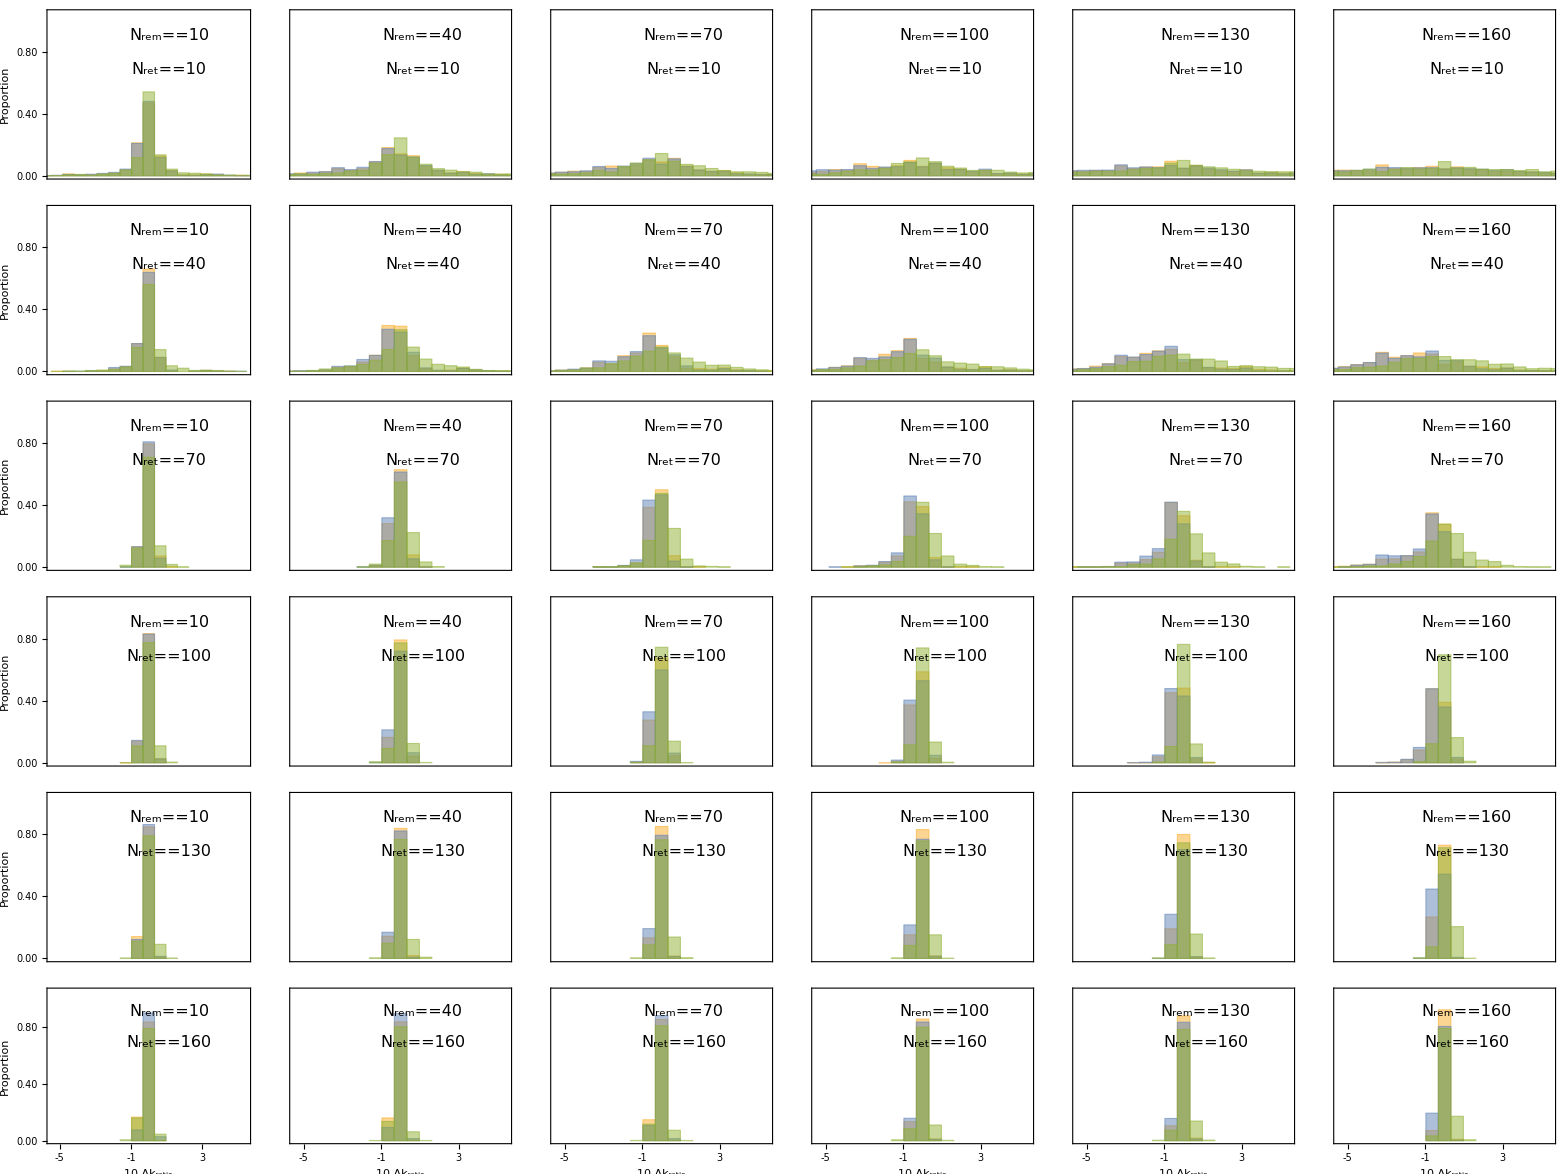

```mathematica
p=Grid[Table[ticks={{If[remove==10,Table[{i,PaddedForm[i,{2,2}]},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]],Table[{i,""},{i,0,1,0.2}]},{If[keep==160,Table[{i,Round[10*i]},{i,-0.5,0.5,0.2}],Table[{i,""},{i,-0.5,0.5,0.2}]],Table[{i,""},{i,-0.5,0.5,0.2}]}};
labels={{If[remove==10,"Proportion",None],None},{If[keep==160,Subscript[Δk,"ratio"]*10,None],None}};
imageSize={If[remove==10,250,250-70],If[keep==160,220,220-40]};
imagePadding={{If[remove==10,75,5],5},{If[keep==160,55,10],1}};Histogram[{Log[Cases[rlst1,u_/;u[[3]]==remove&&u[[4]]==keep][[All,6]]]/Log[10],Log[Cases[rlst2,u_/;u[[3]]==remove&&u[[4]]==keep][[All,6]]]/Log[10],Log[Cases[rlst1,u_/;u[[3]]==remove&&u[[4]]==keep][[All,6]]]/Log[10]-Log[Cases[rlst2,u_/;u[[3]]==remove&&u[[4]]==keep][[All,6]]]/Log[10]},{-1,1,2/31.},"Probability",Axes->False,Frame->True,FrameTicks->ticks,FrameLabel->labels,LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1.5],Black],PlotRange->{{-0.55,0.55},{0,1.05}},AspectRatio->1,ImageSize->imageSize,ImagePadding->imagePadding,PlotRangeClipping->True,Epilog->{Inset[Style[Subscript[N,"rem"]==remove,16],Scaled[{0.6,0.85}]],Inset[Style[Subscript[N,"ret"]==keep,16],Scaled[{0.6,0.65}]]}],{keep,10,160,30},{remove,10,160,30}]]
```

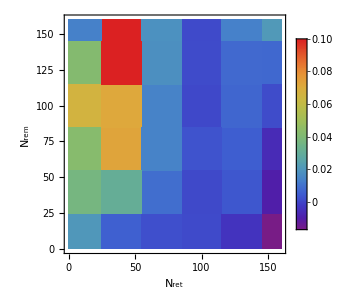
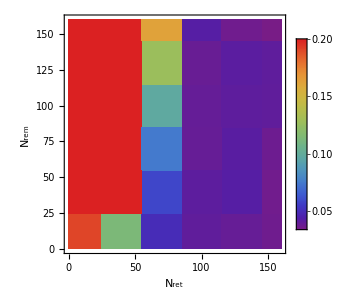
-Graphics- | -Graphics-

stats.pdf

```mathematica
p=Grid[{{ListDensityPlot[Flatten[Table[{keep,remove,Mean[Cases[diff,u_/;u[[1]]==52&&u[[3]]==remove&&u[[4]]==keep&&u[[6]]≠"failed"][[All,6]]]},{keep,10,160,30},{remove,10,160,30}],1],InterpolationOrder->0,FrameLabel->{{Subscript[N,"rem"],None},{Subscript[N,"ret"],Mean[Subscript[Δk,"ratio"]]}},ClippingStyle->Automatic,LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{-0.1,0.1},PlotLegends->True,ImageSize->300,ColorFunction->"Rainbow"],ListDensityPlot[Flatten[Table[{keep,remove,StandardDeviation[Cases[diff,u_/;u[[1]]==52&&u[[3]]==remove&&u[[4]]==keep&&u[[6]]≠"failed"][[All,6]]]},{keep,10,160,30},{remove,10,160,30}],1],InterpolationOrder->0,FrameLabel->{{Subscript[N,"rem"],None},{Subscript[N,"ret"],StandardDeviation[Subscript[Δk,"ratio"]]}},ClippingStyle->Automatic,LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->{0.0,0.2},PlotLegends->True,ImageSize->300,ColorFunction->"Rainbow"]}}]
Export["stats.pdf",p]
```

```mathematica
means37={};
errors37={};
means52={};
errors52={};
senses37={};
senses52={};
Monitor[Do[Do[
cases=Cases[rlst2,u_/;u[[1]]==37&&u[[3]]==remove&&u[[4]]==keep&&Last[u]≠"failed"];If[Length[cases]>0,AppendTo[means37,{keep,remove,Mean[Abs[Log[DeleteCases[cases[[All,6]],u_/;u=="failed"]]/Log[10]]]}];
AppendTo[errors37,{keep,remove,Mean[Log[DeleteCases[cases[[All,7]],u_/;u=="failed"]]/Log[10]]}];AppendTo[senses37,{keep,remove,Mean[DeleteCases[cases[[All,5]],u_/;u=="failed"]/sensitivities[[38]]]}];,AppendTo[means37,{}];
AppendTo[errors37,{}];AppendTo[senses37,{}];];cases=Cases[rlst1,u_/;u[[1]]==52&&u[[3]]==remove&&u[[4]]==keep&&Last[u]≠"failed"];If[Length[cases]>0,AppendTo[means52,{keep,remove,Mean[Abs[Log[DeleteCases[cases[[All,6]],u_/;u=="failed"]]/Log[10]]]}];
AppendTo[errors52,{keep,remove,Mean[Log[DeleteCases[cases[[All,7]],u_/;u=="failed"]]/Log[10]]}];AppendTo[senses52,{keep,remove,Mean[DeleteCases[cases[[All,5]],u_/;u=="failed"]/sensitivities[[53]]]}];,AppendTo[means52,{}];
AppendTo[errors52,{}];AppendTo[senses52,{}];];,{keep,10,160,30}];,{remove,10,160,30}],{keep,remove}]
```

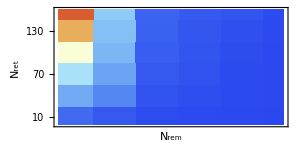
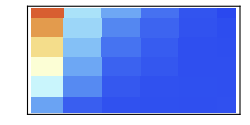
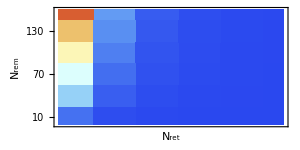
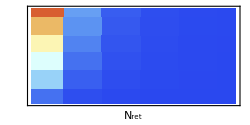
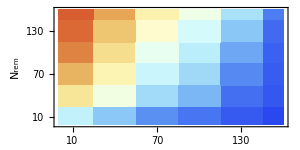
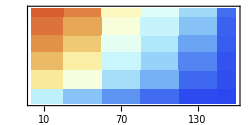
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

averages.pdf

```mathematica
p1=ListDensityPlot[means37,PlotRange->{0,1.0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->300,LabelStyle->Directive[16,Black],FrameLabel->{{Subscript[N,"ret"],None},{Subscript[N,"rem"],"Eq. (I)"}},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,i},{i,10,160,30}],Table[{i,""},{i,10,160,30}]},{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]}},ImagePadding->{{55,10},{5,55}},AspectRatio->1/2];
p2=ListDensityPlot[means52,PlotRange->{0,1.0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->250,LabelStyle->Directive[16,Black],FrameLabel->{{None,None},{None,"Eq. (II)"}},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]},{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]}},ImagePadding->{{5,10},{5,55}},AspectRatio->1/2];
p3=ListDensityPlot[senses37,PlotRange->{0,10.0},ClippingStyle->Automatic,PlotRange->All,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",PlotRange->All,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->300,LabelStyle->Directive[16,Black],FrameLabel->{Subscript[N,"ret"],Subscript[N,"rem"]},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,i},{i,10,160,30}],Table[{i,""},{i,10,160,30}]},{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]}},ImagePadding->{{55,10},{5,5}},AspectRatio->1/2];
p4=ListDensityPlot[senses52,PlotRange->{0,10.0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->250,LabelStyle->Directive[16,Black],FrameLabel->{Subscript[N,"ret"],None},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]},{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]}},ImagePadding->{{5,10},{5,5}},AspectRatio->1/2];
p5=ListDensityPlot[errors37,PlotRange->{-2,0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",PlotRange->All,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->300,LabelStyle->Directive[16,Black],FrameLabel->{Subscript[N,"ret"],Subscript[N,"rem"]},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,i},{i,10,160,30}],Table[{i,""},{i,10,160,30}]},{Table[{i,i},{i,10,160,30}],Table[{i,""},{i,10,160,30}]}},ImagePadding->{{55,10},{55,5}},AspectRatio->1/2];
p6=ListDensityPlot[errors52,PlotRange->{-2,0},ClippingStyle->Automatic,InterpolationOrder->0,ColorFunction->"LightTemperatureMap",ImageSize->250,LabelStyle->Directive[16,Black],FrameLabel->{Subscript[N,"ret"],None},FrameStyle->Directive[AbsoluteThickness[2]],FrameTicks->{{Table[{i,""},{i,10,160,30}],Table[{i,""},{i,10,160,30}]},{Table[{i,i},{i,10,160,30}],Table[{i,""},{i,10,160,30}]}},ImagePadding->{{5,10},{55,5}},AspectRatio->1/2];
p=Grid[{{p1,Grid[{{p2,BarLegend[{"LightTemperatureMap",{0,1.0}},LabelStyle->Directive[Black,14],LegendLabel->Abs[DisplayForm[Subscript[log,10][RowBox[{Subscript[k,est],"/",Subscript[k,0]}]]]],ImageSize->{250,125}]}}]},{p3,Grid[{{p4,BarLegend[{"LightTemperatureMap",{0,10.0}},LabelStyle->Directive[Black,14],LegendLabel->DisplayForm[RowBox[{Subscript[S,"remove"],"/",Subscript[S,"measure"]}]],ImageSize->{250,125}]}}]},{p5,Grid[{{p6,BarLegend[{"LightTemperatureMap",{-2,0}},LabelStyle->Directive[Black,14],LegendLabel->Subscript[log,10][ϵ],ImageSize->{250,125}]}}]}},Alignment->Left]
Export["averages.pdf",p]
```